```mathematica
SetDirectory["/home/s1220054/Dissertation/Dissertation/TiSamp/src"]
```

/home/s1220054/Dissertation/Dissertation/TiSamp/src

```mathematica
phivstime = Import["phitime.txt","CSV"]
```

{{561,-nan},{579,-nan},{593,-nan},{606,-nan},{622,-nan},{633,-nan},{654,1},{670,1},{680,1},{690,0.666667},{701,0.666667},{714,0.666667},{725,0.666667},{740,0.666667},{755,0.75},{768,0.75},{787,0.75},{796,0.6},{810,0.666667},{819,0.666667},{829,0.666667},{846,0.666667},{860,0.666667},{869,0.714286},{878,0.714286},{892,0.714286},{908,0.714286},{923,0.714286},{937,0.714286},{946,0.714286},{962,0.75},{969,0.75},{979,0.777778},{992,0.777778},{1002,0.777778},{1010,0.818182},{1020,0.818182},{1028,0.818182},{1038,0.818182},{1043,0.818182},{1059,0.818182},{1067,0.818182},{1082,0.769231},{1088,0.769231},{1101,0.769231},{1114,0.769231},{1125,0.769231},{1140,0.785714},{1157,0.785714},{1168,0.785714},{1181,0.785714},{1190,0.733333},{1201,0.733333},{1213,0.733333},{1224,0.705882},{1241,0.705882},{1251,0.705882},{1260,0.705882},{1272,0.705882},{1281,0.705882},{1293,0.722222},{1304,0.722222},{1313,0.684211},{1323,0.684211},{1331,0.684211},{1338,0.684211},{1353,0.7},{1364,0.714286},{1372,0.714286},{1377,0.681818},{1388,0.681818},{1395,0.681818},{1407,0.681818},{1416,0.681818},{1430,0.681818},{1443,0.681818},{1454,0.681818},{1466,0.681818},{1474,0.681818},{1480,0.681818},{1490,0.681818},{1498,0.681818},{1505,0.681818},{1513,0.681818},{1522,0.681818},{1533,0.681818},{1540,0.666667},{1547,0.666667},{1553,0.666667},{1566,0.64},{1576,0.653846},{1584,0.653846},{1590,0.653846},{1596,0.653846},{1607,0.62963},{1615,0.62963},{1619,0.62963},{1623,0.607143},{1633,0.607143},{1639,0.607143},{1648,0.607143},{1663,0.607143},{1672,0.607143},{1680,0.607143},{1690,0.62069},{1705,0.62069},{1717,0.62069},{1728,0.645161},{1737,0.645161},{1749,0.625},{1758,0.625},{1767,0.625},{1774,0.625},{1781,0.636364},{1788,0.636364},{1800,0.636364},{1812,0.636364},{1823,0.636364},{1833,0.617647},{1842,0.638889},{1854,0.648649},{1863,0.648649},{1868,0.631579},{1879,0.631579},{1892,0.641026},{1902,0.641026},{1910,0.641026},{1918,0.641026},{1923,0.641026},{1926,0.641026},{1934,0.641026},{1944,0.641026},{1954,0.641026},{1963,0.65},{1972,0.634146},{1984,0.642857},{1989,0.642857},{1999,0.642857},{2010,0.651163},{2017,0.622222},{2030,0.608696},{2038,0.604167},{2045,0.604167},{2054,0.604167},{2066,0.604167},{2078,0.604167},{2092,0.604167},{2097,0.607843},{2104,0.615385},{2112,0.622642},{2119,0.622642},{2123,0.611111},{2131,0.611111},{2141,0.611111},{2147,0.611111},{2159,0.618182},{2167,0.625},{2174,0.625},{2182,0.603448},{2188,0.59322},{2193,0.590164},{2205,0.596774},{2215,0.596774},{2228,0.59375},{2238,0.59375},{2249,0.59375},{2259,0.59375},{2265,0.606061},{2271,0.617647},{2276,0.617647},{2283,0.608696},{2296,0.6},{2307,0.597222},{2314,0.60274},{2326,0.60274},{2330,0.60274},{2340,0.576923},{2348,0.576923},{2357,0.576923},{2368,0.576923},{2374,0.582278},{2378,0.582278},{2388,0.582278},{2398,0.582278},{2406,0.582278},{2419,0.582278},{2427,0.582278},{2433,0.575},{2441,0.560976},{2452,0.571429},{2465,0.563218},{2471,0.563218},{2483,0.561798},{2492,0.561798},{2501,0.561798},{2518,0.555556},{2522,0.554348},{2528,0.554348},{2534,0.554348},{2541,0.554348},{2549,0.554348},{2554,0.547368},{2556,0.541667},{2565,0.546392},{2575,0.546392},{2582,0.540816},{2592,0.540816},{2606,0.540816},{2618,0.540816},{2624,0.535354},{2633,0.535354},{2641,0.54902},{2654,0.54902},{2662,0.54902},{2670,0.553398},{2676,0.552381},{2684,0.54717},{2690,0.546296},{2702,0.540541},{2709,0.535714},{2715,0.539823},{2721,0.54386},{2728,0.53913},{2732,0.53913},{2738,0.543103},{2743,0.543103},{2749,0.543103},{2751,0.538462},{2759,0.533898},{2768,0.537815},{2774,0.537815},{2783,0.537815},{2793,0.541667},{2796,0.541667},{2805,0.545455},{2815,0.536585},{2822,0.536},{2830,0.539683},{2841,0.539683},{2853,0.53125},{2861,0.527132},{2873,0.527132},{2879,0.530769},{2888,0.530769},{2891,0.526316},{2899,0.526316},{2903,0.529851},{2910,0.536765},{2916,0.536765},{2922,0.536232},{2930,0.539568},{2938,0.546099},{2942,0.542254},{2949,0.542254},{2959,0.542254},{2969,0.538462},{2974,0.538462},{2978,0.541667},{2987,0.541667},{2993,0.547945},{2999,0.547297},{3004,0.543046},{3013,0.543046},{3020,0.535948},{3025,0.535948},{3031,0.532468},{3039,0.532468},{3047,0.532468},{3054,0.532051},{3064,0.531646},{3071,0.531646},{3075,0.53125},{3084,0.534161},{3093,0.534161},{3098,0.534161},{3103,0.530488},{3110,0.530488},{3121,0.530488},{3137,0.527273},{3144,0.527273},{3148,0.527273},{3157,0.532934},{3164,0.532934},{3169,0.532934},{3175,0.532934},{3183,0.538012},{3191,0.543353},{3194,0.545977},{3201,0.545977},{3207,0.545977},{3215,0.545977},{3221,0.542857},{3226,0.542857},{3232,0.545455},{3235,0.548023},{3242,0.544944},{3246,0.544444},{3252,0.549451},{3259,0.549451},{3263,0.549451},{3276,0.545946},{3286,0.550802},{3288,0.547872},{3291,0.550265},{3296,0.550265},{3298,0.550265},{3306,0.554974},{3314,0.554974},{3323,0.552083},{3329,0.549223},{3334,0.549223},{3341,0.549223},{3347,0.556122},{3354,0.556122},{3360,0.558376},{3365,0.558376},{3376,0.558376},{3380,0.555556},{3389,0.552764},{3396,0.552764},{3400,0.555},{3411,0.557214},{3421,0.561576},{3428,0.561576},{3435,0.561576},{3441,0.560976},{3450,0.555556},{3455,0.557692},{3468,0.557692},{3473,0.557692},{3487,0.557692},{3496,0.557692},{3507,0.557692},{3516,0.557692},{3521,0.555024},{3528,0.559242},{3538,0.559242},{3546,0.556604},{3552,0.558685},{3559,0.556075},{3564,0.55814},{3568,0.55814},{3579,0.555046},{3591,0.557078},{3597,0.559091},{3601,0.561086},{3607,0.560538},{3611,0.56},{3616,0.563877},{3622,0.561404},{3624,0.561404},{3632,0.563319},{3641,0.56087},{3648,0.56087},{3653,0.556034},{3663,0.555556},{3670,0.557447},{3678,0.557447},{3682,0.557447},{3693,0.555085},{3700,0.554622},{3710,0.552301},{3715,0.554167},{3720,0.556017},{3724,0.556017},{3730,0.555556},{3736,0.559184},{3742,0.559184},{3748,0.556911},{3754,0.558704},{3761,0.558704},{3768,0.56},{3780,0.56},{3784,0.56},{3791,0.56},{3799,0.557769},{3807,0.557769},{3814,0.557769},{3821,0.555556},{3828,0.556863},{3839,0.556863},{3845,0.558594},{3849,0.562016},{3859,0.561069},{3862,0.558935},{3875,0.560606},{3886,0.560606},{3888,0.558491},{3893,0.558491},{3898,0.56015},{3903,0.558052},{3912,0.55597},{3918,0.557621},{3925,0.557621},{3931,0.557621},{3935,0.557621},{3941,0.557621},{3948,0.557621},{3950,0.555556},{3956,0.555556},{3960,0.555556},{3966,0.557196},{3972,0.558824},{3975,0.56044},{3979,0.562044},{3985,0.562044},{3989,0.56},{3994,0.56},{3998,0.563177},{4005,0.564748},{4010,0.566308},{4014,0.564286},{4020,0.562278},{4028,0.561404},{4034,0.555556},{4039,0.555556},{4045,0.558621},{4050,0.558621},{4057,0.561644},{4062,0.561644},{4068,0.559727},{4078,0.552189},{4084,0.552189},{4089,0.550336},{4095,0.550336},{4103,0.550336},{4111,0.551839},{4116,0.553333},{4122,0.553333},{4129,0.553333},{4137,0.549669},{4141,0.547855},{4146,0.55082},{4150,0.55082},{4156,0.54902},{4164,0.547231},{4168,0.545161},{4175,0.546624},{4183,0.542857},{4187,0.544025},{4191,0.546875},{4200,0.546875},{4206,0.547988},{4213,0.546296},{4216,0.546296},{4224,0.544615},{4229,0.544615},{4235,0.546012},{4239,0.54878},{4243,0.550152},{4249,0.552553},{4254,0.553892},{4257,0.553892},{4262,0.550595},{4275,0.550595},{4280,0.550595},{4289,0.550595},{4295,0.550595},{4300,0.548961},{4306,0.548673},{4312,0.548387},{4318,0.546784},{4320,0.546784},{4324,0.546784},{4331,0.548105},{4341,0.549419},{4348,0.550432},{4353,0.550143},{4355,0.551429},{4361,0.551429},{4371,0.553977},{4374,0.555241},{4379,0.555241},{4384,0.555241},{4387,0.558659},{4394,0.558659},{4399,0.559889},{4405,0.559557},{4409,0.560773},{4413,0.563187},{4417,0.562842},{4424,0.562842},{4430,0.563686},{4438,0.561828},{4441,0.561828},{4448,0.561828},{4451,0.563003},{4456,0.564171},{4460,0.564171},{4465,0.562334},{4470,0.562334},{4477,0.560847},{4485,0.557895},{4493,0.557895},{4497,0.558747},{4500,0.559896},{4508,0.559585},{4513,0.559585},{4521,0.561856},{4528,0.562982},{4532,0.561538},{4539,0.56266},{4542,0.560914},{4547,0.563131},{4556,0.565327},{4560,0.565327},{4565,0.565327},{4569,0.565327},{4576,0.565327},{4580,0.566416},{4585,0.566085},{4593,0.566085},{4597,0.567164},{4601,0.565757},{4603,0.562963},{4614,0.564039},{4619,0.563725},{4622,0.563725},{4629,0.564477},{4640,0.563855},{4650,0.564904},{4659,0.565632},{4669,0.565632},{4673,0.565632},{4679,0.565321},{4685,0.566351},{4689,0.567059},{4696,0.567059},{4701,0.567059},{4707,0.569087},{4714,0.570093},{4719,0.571096},{4727,0.569767},{4734,0.570766},{4737,0.570766},{4740,0.570766},{4747,0.568129},{4749,0.567816},{4760,0.567506},{4765,0.568493},{4773,0.568182},{4779,0.568182},{4780,0.569161},{4784,0.567873},{4791,0.567873},{4798,0.567568},{4802,0.567568},{4804,0.568539},{4811,0.569507},{4820,0.570156},{4821,0.568889},{4827,0.569536},{4832,0.569536},{4835,0.570485},{4839,0.569231},{4844,0.569231},{4848,0.569231},{4853,0.569231},{4856,0.56427},{4862,0.564655},{4868,0.564655},{4873,0.564655},{4881,0.564655},{4884,0.565591},{4888,0.566524},{4890,0.56531},{4894,0.566239},{4896,0.565032},{4905,0.56383},{4913,0.56383},{4922,0.564756},{4926,0.565678},{4933,0.564211},{4938,0.563025},{4945,0.564315},{4950,0.56701},{4957,0.565844},{4962,0.565574},{4964,0.565306},{4966,0.567073},{4971,0.567951},{4977,0.566802},{4981,0.567677},{4990,0.562},{4992,0.562},{4997,0.560636},{5000,0.560396},{5002,0.560396},{5007,0.560158},{5010,0.559055},{5017,0.558594},{5020,0.558366},{5026,0.558366},{5029,0.558366},{5034,0.560078},{5038,0.560928},{5047,0.560694},{5049,0.560694},{5056,0.559615},{5059,0.559615},{5064,0.559387},{5069,0.560229},{5076,0.55916},{5081,0.557875},{5088,0.557656},{5096,0.557656},{5101,0.557439},{5111,0.558271},{5119,0.560748},{5124,0.559701},{5128,0.560521},{5135,0.560521},{5141,0.561111},{5145,0.561922},{5152,0.561694},{5160,0.561468},{5166,0.561468},{5167,0.56044},{5177,0.560219},{5187,0.56},{5191,0.558984},{5196,0.558984},{5201,0.560579},{5208,0.560579},{5213,0.560579},{5219,0.559567},{5224,0.557348},{5230,0.556351},{5234,0.557143},{5239,0.55615},{5246,0.55615},{5250,0.55615},{5252,0.55516},{5256,0.554965},{5258,0.556537},{5261,0.556338},{5263,0.557118},{5268,0.557118},{5274,0.558669},{5278,0.557692},{5279,0.556719},{5285,0.556522},{5291,0.556522},{5296,0.553633},{5304,0.554404},{5308,0.552496},{5314,0.552316},{5319,0.55137},{5325,0.549488},{5330,0.548061},{5333,0.548061},{5341,0.54958},{5346,0.550336},{5350,0.550336},{5354,0.550918},{5359,0.55},{5372,0.550749},{5376,0.548922},{5382,0.549505},{5387,0.549505},{5393,0.5486},{5402,0.54844},{5409,0.54844},{5416,0.547541},{5422,0.548282},{5426,0.548124},{5428,0.548124},{5433,0.547231},{5441,0.547967},{5446,0.547812},{5451,0.547812},{5455,0.549114},{5465,0.549679},{5471,0.547923},{5477,0.547771},{5482,0.548336},{5482,0.549051},{5484,0.547319},{5492,0.548742},{5497,0.547881},{5504,0.547881},{5512,0.546022},{5517,0.546022},{5521,0.546022},{5527,0.546022},{5534,0.545879},{5540,0.546584},{5547,0.54644},{5555,0.545595},{5560,0.545455},{5565,0.546708},{5569,0.546708},{5578,0.545038},{5583,0.54697},{5591,0.54697},{5599,0.547655},{5602,0.546687},{5612,0.546687},{5618,0.545865},{5626,0.54559},{5633,0.544776},{5635,0.544643},{5642,0.545994},{5648,0.545858},{5650,0.544787},{5656,0.544787},{5658,0.544656},{5662,0.544656},{5667,0.545322},{5674,0.545058},{5681,0.546377},{5686,0.548341},{5690,0.54755},{5695,0.548711},{5697,0.548711},{5706,0.547143},{5710,0.549075},{5713,0.548798},{5716,0.548798},{5725,0.550071},{5731,0.550704},{5739,0.551336},{5745,0.551966},{5755,0.551966},{5758,0.553221},{5762,0.553221},{5770,0.552301},{5774,0.551532},{5782,0.551389},{5788,0.552632},{5791,0.553867},{5797,0.554483},{5802,0.554483},{5809,0.554333},{5814,0.554795},{5816,0.554795},{5821,0.554795},{5826,0.556011},{5828,0.555102},{5832,0.555707},{5835,0.555707},{5842,0.554953},{5845,0.556157},{5847,0.554656},{5852,0.555256},{5857,0.554509},{5861,0.553763},{5867,0.554362},{5879,0.552878},{5883,0.553476},{5888,0.554072},{5896,0.553333},{5902,0.552597},{5903,0.552457},{5912,0.551724},{5916,0.552318},{5918,0.552318},{5925,0.55291},{5929,0.55218},{5935,0.552042},{5939,0.552042},{5942,0.551905},{5949,0.551769},{5953,0.551047},{5957,0.551499},{5960,0.550065},{5965,0.549223},{5968,0.549806},{5970,0.549096},{5974,0.548969},{5978,0.548263},{5987,0.548139},{5990,0.548015},{6001,0.548469},{6004,0.548346},{6010,0.548796},{6019,0.549242},{6022,0.549811},{6027,0.549686},{6035,0.548872},{6042,0.548872},{6047,0.549437},{6051,0.549875},{6054,0.550436},{6059,0.550436},{6061,0.550995},{6068,0.550868},{6071,0.550743},{6075,0.550617},{6083,0.551046},{6088,0.55092},{6094,0.5489},{6097,0.550548},{6101,0.551095},{6104,0.55164},{6107,0.550971},{6111,0.548972},{6114,0.548309},{6118,0.548193},{6123,0.549279},{6133,0.55036},{6140,0.548387},{6144,0.547733},{6146,0.547733},{6153,0.54708},{6158,0.546856},{6163,0.546856},{6168,0.547393},{6178,0.547929},{6183,0.547929},{6187,0.547929},{6188,0.548463},{6196,0.548881},{6204,0.548122},{6216,0.546838},{6219,0.545984},{6223,0.545877},{6230,0.546404},{6233,0.546404},{6236,0.545035},{6240,0.545035},{6246,0.544406},{6246,0.544304},{6252,0.54535},{6261,0.543478},{6269,0.543379},{6272,0.542759},{6280,0.541524},{6285,0.541524},{6295,0.542373},{6304,0.54115},{6312,0.54115},{6318,0.539843},{6324,0.539843},{6326,0.540873},{6333,0.540179},{6339,0.540179},{6343,0.540691},{6348,0.54},{6355,0.540421},{6363,0.540929},{6367,0.540929},{6373,0.540929},{6381,0.540929},{6382,0.540749},{6387,0.540749},{6395,0.540066},{6401,0.54057},{6405,0.539978},{6408,0.539978},{6415,0.53821},{6419,0.538629},{6426,0.54013},{6430,0.540628},{6435,0.541126},{6440,0.539957},{6447,0.540366},{6452,0.54086},{6456,0.541845},{6461,0.541176},{6467,0.541578},{6468,0.541977},{6477,0.541314},{6483,0.541226},{6490,0.540569},{6494,0.540966},{6498,0.541361},{6508,0.540795},{6516,0.539583},{6521,0.540456},{6525,0.540456},{6533,0.540456},{6537,0.539896},{6542,0.539814},{6546,0.538144},{6549,0.539014},{6553,0.53791},{6559,0.537359},{6565,0.537832},{6567,0.539246},{6572,0.539246},{6581,0.538618},{6585,0.538071},{6590,0.537449},{6597,0.536831},{6602,0.537764},{6607,0.538229},{6613,0.537688},{6622,0.537149},{6625,0.537074},{6629,0.537463},{6629,0.536853},{6636,0.536706},{6639,0.537166},{6642,0.537166},{6647,0.537166},{6655,0.537549},{6663,0.538006},{6666,0.537475},{6671,0.536946},{6675,0.536873},{6683,0.536873},{6683,0.536873},{6688,0.537782},{6693,0.538688},{6698,0.540039},{6700,0.540039},{6711,0.540039},{6722,0.540488},{6725,0.540488},{6729,0.540936},{6734,0.540777},{6737,0.540252},{6743,0.539206},{6748,0.538536},{6756,0.537944},{6762,0.537428},{6767,0.536913},{6773,0.536913},{6779,0.537356},{6786,0.537799},{6791,0.538241},{6799,0.538682},{6803,0.538682},{6808,0.539561},{6811,0.539411},{6816,0.540284},{6822,0.540132},{6830,0.540566},{6833,0.540057},{6836,0.54049},{6838,0.540414},{6841,0.539906},{6850,0.539906},{6852,0.538821},{6858,0.538318},{6861,0.538318},{6865,0.537244},{6871,0.536744},{6877,0.537175},{6883,0.538033},{6886,0.537963},{6898,0.53839},{6900,0.53839},{6907,0.53839},{6910,0.53839},{6912,0.537327},{6915,0.537684},{6920,0.536205},{6929,0.53663},{6932,0.53663},{6937,0.537054},{6945,0.536563},{6953,0.536919},{6957,0.536852},{6961,0.537205},{6965,0.537138},{6976,0.537004},{6980,0.536519},{6985,0.536937},{6993,0.536388},{7003,0.536804},{7008,0.536323},{7011,0.536738},{7015,0.536258},{7018,0.536128},{7022,0.535111},{7031,0.534574},{7039,0.534574},{7040,0.534101},{7045,0.534925},{7052,0.533981},{7055,0.534802},{7061,0.535558},{7067,0.535965},{7074,0.535965}}

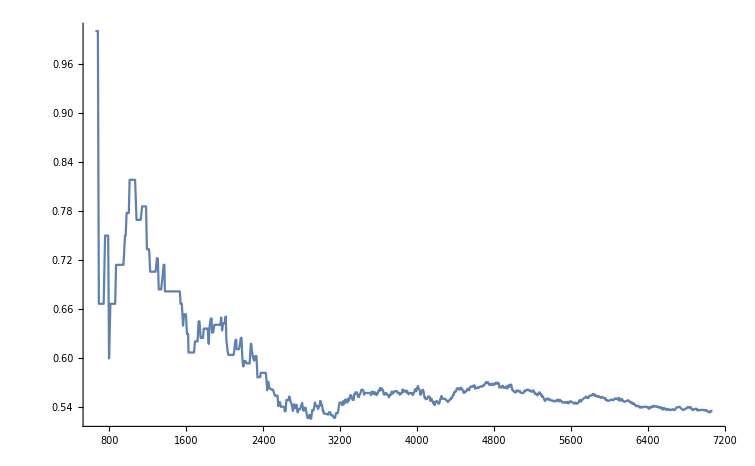

```mathematica
ListLinePlot[phivstime, PlotRange->All]
```

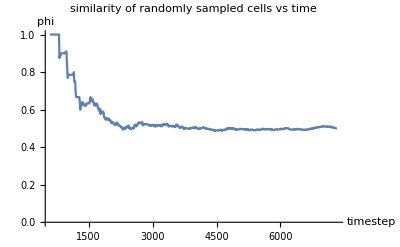

```mathematica
Show[%30,AxesLabel->{HoldForm[timestep],HoldForm[phi]},
PlotLabel->HoldForm[similarity of randomly sampled cells vs time],LabelStyle->{GrayLevel[0]}]
```

```mathematica
firstsnaptype1 = Import["new2.txt","CSV"]
```

{{276,297},{277,296},{277,297},{277,298},{277,299},{277,300},{277,301},{277,302},{277,308},{278,296},{278,297},{278,298},{278,299},{278,300},{278,301},{278,302},{278,303},{278,304},{278,308},{278,309},{278,310},{278,311},{278,312},{279,286},{279,288},{279,291},{279,292},{279,293},{279,294},{279,295},{279,296},{279,297},{279,298},{279,299},{279,300},{279,301},{279,302},{279,303},{279,304},{279,305},{279,306},{279,307},{279,308},{279,309},{279,310},{279,311},{279,312},{279,313},{279,314},{280,284},{280,285},{280,286},{280,287},{280,288},{280,289},{280,290},{280,292},{280,293},{280,294},{280,295},{280,297},{280,298},{280,299},{280,300},{280,301},{280,302},{280,303},{280,304},{280,305},{280,306},{280,307},{280,309},{280,310},{280,311},{280,312},{281,287},{281,288},{281,289},{281,290},{281,291},{281,292},{281,293},{281,294},{281,295},{281,297},{281,298},{281,300},{281,301},{281,302},{281,303},{281,304},{281,305},{281,306},{281,307},{281,308},{281,309},{281,310},{281,311},{281,312},{281,313},{281,314},{281,316},{282,282},{282,283},{282,284},{282,286},{282,287},{282,288},{282,289},{282,290},{282,291},{282,292},{282,294},{282,295},{282,296},{282,297},{282,298},{282,299},{282,300},{282,301},{282,302},{282,303},{282,305},{282,306},{282,307},{282,308},{282,309},{282,310},{282,311},{282,312},{282,313},{282,314},{282,315},{282,317},{283,279},{283,280},{283,282},{283,283},{283,284},{283,286},{283,287},{283,289},{283,290},{283,291},{283,292},{283,293},{283,294},{283,295},{283,296},{283,298},{283,299},{283,300},{283,301},{283,304},{283,306},{283,307},{283,308},{283,309},{283,310},{283,312},{283,313},{283,314},{283,315},{283,316},{283,318},{284,275},{284,280},{284,281},{284,282},{284,283},{284,284},{284,286},{284,287},{284,288},{284,289},{284,290},{284,291},{284,293},{284,294},{284,295},{284,296},{284,297},{284,298},{284,299},{284,300},{284,301},{284,302},{284,303},{284,305},{284,306},{284,307},{284,308},{284,309},{284,310},{284,311},{284,312},{284,313},{284,314},{284,315},{284,317},{284,318},{284,319},{284,320},{284,322},{285,272},{285,273},{285,274},{285,275},{285,276},{285,277},{285,278},{285,279},{285,280},{285,281},{285,282},{285,283},{285,284},{285,285},{285,286},{285,287},{285,288},{285,289},{285,290},{285,291},{285,292},{285,293},{285,294},{285,295},{285,296},{285,297},{285,298},{285,299},{285,300},{285,302},{285,304},{285,306},{285,307},{285,308},{285,309},{285,310},{285,311},{285,312},{285,313},{285,314},{285,315},{285,316},{285,317},{285,318},{285,319},{285,320},{285,321},{285,322},{285,323},{286,270},{286,271},{286,272},{286,273},{286,274},{286,275},{286,276},{286,277},{286,279},{286,280},{286,281},{286,282},{286,283},{286,284},{286,286},{286,287},{286,288},{286,290},{286,291},{286,292},{286,293},{286,294},{286,295},{286,298},{286,299},{286,301},{286,303},{286,305},{286,307},{286,309},{286,310},{286,311},{286,312},{286,313},{286,314},{286,315},{286,316},{286,317},{286,318},{286,319},{286,320},{286,321},{286,322},{287,271},{287,272},{287,273},{287,274},{287,275},{287,276},{287,277},{287,278},{287,280},{287,281},{287,282},{287,283},{287,285},{287,286},{287,287},{287,288},{287,289},{287,290},{287,293},{287,294},{287,296},{287,297},{287,298},{287,299},{287,300},{287,301},{287,302},{287,303},{287,304},{287,306},{287,307},{287,309},{287,310},{287,311},{287,312},{287,313},{287,314},{287,315},{287,316},{287,317},{287,318},{287,319},{287,320},{287,321},{287,322},{287,324},{287,325},{288,271},{288,273},{288,274},{288,275},{288,276},{288,277},{288,278},{288,279},{288,280},{288,281},{288,282},{288,284},{288,285},{288,286},{288,287},{288,288},{288,289},{288,291},{288,292},{288,293},{288,294},{288,295},{288,296},{288,297},{288,298},{288,300},{288,302},{288,303},{288,304},{288,305},{288,306},{288,307},{288,308},{288,309},{288,310},{288,311},{288,312},{288,313},{288,316},{288,317},{288,318},{288,319},{288,320},{288,322},{288,323},{288,324},{288,325},{288,326},{289,272},{289,273},{289,274},{289,275},{289,276},{289,277},{289,278},{289,280},{289,282},{289,283},{289,284},{289,285},{289,286},{289,287},{289,288},{289,289},{289,290},{289,292},{289,293},{289,295},{289,296},{289,297},{289,298},{289,300},{289,301},{289,302},{289,304},{289,305},{289,306},{289,307},{289,308},{289,310},{289,312},{289,313},{289,314},{289,315},{289,316},{289,317},{289,318},{289,319},{289,320},{289,321},{289,322},{289,323},{289,324},{289,325},{289,326},{289,327},{289,328},{290,272},{290,273},{290,274},{290,275},{290,277},{290,278},{290,279},{290,284},{290,285},{290,286},{290,287},{290,289},{290,290},{290,291},{290,294},{290,295},{290,296},{290,297},{290,299},{290,300},{290,301},{290,302},{290,303},{290,304},{290,306},{290,311},{290,313},{290,314},{290,315},{290,317},{290,318},{290,319},{290,320},{290,321},{290,323},{290,324},{290,325},{290,326},{291,271},{291,272},{291,273},{291,274},{291,275},{291,276},{291,277},{291,278},{291,280},{291,282},{291,284},{291,285},{291,286},{291,287},{291,290},{291,292},{291,297},{291,301},{291,302},{291,303},{291,304},{291,305},{291,306},{291,308},{291,311},{291,312},{291,313},{291,316},{291,317},{291,318},{291,319},{291,320},{291,321},{291,322},{291,323},{291,324},{291,325},{291,326},{291,327},{291,328},{292,270},{292,271},{292,272},{292,273},{292,274},{292,275},{292,276},{292,277},{292,278},{292,280},{292,282},{292,284},{292,285},{292,286},{292,287},{292,289},{292,290},{292,291},{292,292},{292,295},{292,296},{292,297},{292,299},{292,300},{292,304},{292,305},{292,306},{292,307},{292,308},{292,309},{292,310},{292,312},{292,315},{292,317},{292,318},{292,320},{292,321},{292,322},{292,323},{292,324},{292,325},{292,326},{292,327},{293,272},{293,273},{293,274},{293,275},{293,276},{293,278},{293,279},{293,282},{293,283},{293,284},{293,285},{293,287},{293,288},{293,289},{293,290},{293,292},{293,293},{293,294},{293,295},{293,296},{293,297},{293,298},{293,299},{293,300},{293,301},{293,302},{293,303},{293,304},{293,305},{293,307},{293,310},{293,311},{293,313},{293,314},{293,315},{293,316},{293,318},{293,319},{293,320},{293,321},{293,322},{293,323},{293,324},{293,325},{293,326},{293,327},{294,269},{294,270},{294,271},{294,272},{294,273},{294,274},{294,275},{294,276},{294,277},{294,278},{294,279},{294,280},{294,281},{294,282},{294,283},{294,284},{294,285},{294,286},{294,287},{294,289},{294,290},{294,292},{294,293},{294,294},{294,295},{294,296},{294,298},{294,301},{294,302},{294,303},{294,304},{294,305},{294,306},{294,307},{294,309},{294,310},{294,311},{294,312},{294,313},{294,314},{294,317},{294,318},{294,319},{294,320},{294,321},{294,322},{294,323},{294,324},{295,270},{295,271},{295,272},{295,273},{295,274},{295,275},{295,276},{295,277},{295,278},{295,279},{295,280},{295,281},{295,282},{295,283},{295,284},{295,285},{295,286},{295,287},{295,288},{295,290},{295,292},{295,294},{295,295},{295,296},{295,297},{295,298},{295,299},{295,301},{295,302},{295,305},{295,306},{295,309},{295,310},{295,311},{295,312},{295,316},{295,317},{295,318},{295,319},{295,320},{295,321},{295,322},{295,323},{295,324},{295,325},{296,267},{296,268},{296,270},{296,271},{296,272},{296,273},{296,274},{296,275},{296,276},{296,277},{296,278},{296,279},{296,280},{296,281},{296,282},{296,283},{296,284},{296,285},{296,287},{296,288},{296,289},{296,290},{296,291},{296,292},{296,294},{296,296},{296,297},{296,305},{296,308},{296,309},{296,310},{296,313},{296,315},{296,316},{296,317},{296,319},{296,320},{296,323},{296,324},{296,325},{296,326},{297,267},{297,268},{297,269},{297,270},{297,271},{297,272},{297,273},{297,274},{297,275},{297,276},{297,278},{297,280},{297,281},{297,282},{297,283},{297,285},{297,286},{297,287},{297,288},{297,291},{297,292},{297,293},{297,294},{297,296},{297,297},{297,298},{297,299},{297,300},{297,301},{297,303},{297,304},{297,306},{297,307},{297,308},{297,310},{297,312},{297,313},{297,314},{297,315},{297,318},{297,319},{297,320},{297,321},{297,322},{297,323},{297,324},{297,325},{298,264},{298,265},{298,266},{298,267},{298,268},{298,269},{298,270},{298,271},{298,272},{298,275},{298,276},{298,278},{298,279},{298,280},{298,281},{298,283},{298,284},{298,285},{298,293},{298,296},{298,297},{298,299},{298,301},{298,304},{298,305},{298,306},{298,307},{298,308},{298,309},{298,311},{298,313},{298,314},{298,315},{298,317},{298,318},{298,319},{298,320},{298,321},{298,322},{298,323},{298,324},{298,325},{298,326},{299,266},{299,267},{299,268},{299,269},{299,270},{299,271},{299,272},{299,273},{299,274},{299,276},{299,277},{299,278},{299,279},{299,280},{299,283},{299,284},{299,285},{299,286},{299,287},{299,288},{299,289},{299,290},{299,293},{299,294},{299,295},{299,297},{299,303},{299,304},{299,306},{299,307},{299,309},{299,310},{299,312},{299,313},{299,314},{299,315},{299,317},{299,318},{299,319},{299,320},{299,321},{299,322},{299,323},{299,324},{299,325},{300,266},{300,267},{300,268},{300,269},{300,270},{300,271},{300,272},{300,273},{300,274},{300,275},{300,276},{300,277},{300,278},{300,279},{300,280},{300,282},{300,283},{300,284},{300,287},{300,289},{300,291},{300,292},{300,294},{300,299},{300,300},{300,301},{300,306},{300,309},{300,311},{300,313},{300,314},{300,315},{300,317},{300,318},{300,319},{300,320},{300,321},{300,323},{300,324},{300,325},{300,326},{300,327},{300,328},{300,329},{301,266},{301,268},{301,269},{301,270},{301,271},{301,273},{301,274},{301,275},{301,276},{301,277},{301,278},{301,279},{301,280},{301,283},{301,284},{301,285},{301,286},{301,287},{301,289},{301,291},{301,292},{301,294},{301,295},{301,297},{301,298},{301,304},{301,307},{301,309},{301,310},{301,311},{301,312},{301,314},{301,316},{301,317},{301,318},{301,319},{301,321},{301,322},{301,323},{301,324},{301,325},{301,326},{301,327},{301,328},{301,329},{301,330},{302,266},{302,267},{302,268},{302,269},{302,270},{302,271},{302,272},{302,273},{302,274},{302,275},{302,276},{302,277},{302,278},{302,279},{302,280},{302,281},{302,282},{302,284},{302,286},{302,287},{302,289},{302,290},{302,292},{302,293},{302,295},{302,296},{302,309},{302,311},{302,316},{302,319},{302,320},{302,321},{302,323},{302,324},{302,325},{302,326},{303,268},{303,270},{303,271},{303,272},{303,274},{303,275},{303,276},{303,277},{303,279},{303,280},{303,283},{303,284},{303,285},{303,287},{303,288},{303,290},{303,291},{303,292},{303,293},{303,294},{303,297},{303,298},{303,299},{303,300},{303,302},{303,310},{303,312},{303,315},{303,317},{303,319},{303,320},{303,321},{303,324},{304,271},{304,272},{304,274},{304,275},{304,277},{304,278},{304,281},{304,285},{304,289},{304,290},{304,292},{304,294},{304,295},{304,297},{304,298},{304,299},{304,300},{304,303},{304,304},{304,306},{304,309},{304,313},{304,314},{304,317},{304,321},{304,328},{305,276},{305,277},{305,278},{305,279},{305,280},{305,283},{305,284},{305,285},{305,286},{305,287},{305,289},{305,290},{305,291},{305,292},{305,294},{305,295},{305,296},{305,297},{305,298},{305,299},{305,301},{305,303},{305,306},{305,307},{305,308},{305,322},{305,324},{306,271},{306,272},{306,273},{306,274},{306,278},{306,280},{306,281},{306,282},{306,283},{306,285},{306,286},{306,287},{306,288},{306,290},{306,292},{306,293},{306,296},{306,301},{306,302},{306,303},{306,306},{306,309},{306,311},{306,316},{307,269},{307,270},{307,271},{307,272},{307,273},{307,275},{307,277},{307,280},{307,281},{307,282},{307,283},{307,284},{307,285},{307,286},{307,287},{307,288},{307,290},{307,291},{307,292},{307,293},{307,295},{307,296},{307,297},{307,298},{307,299},{307,300},{307,308},{307,309},{307,310},{307,313},{307,315},{307,317},{307,320},{308,268},{308,269},{308,270},{308,271},{308,272},{308,274},{308,276},{308,277},{308,278},{308,279},{308,280},{308,284},{308,287},{308,288},{308,290},{308,291},{308,292},{308,293},{308,294},{308,295},{308,299},{308,300},{308,301},{308,302},{308,306},{309,267},{309,268},{309,269},{309,270},{309,271},{309,272},{309,273},{309,274},{309,275},{309,276},{309,277},{309,278},{309,279},{309,280},{309,281},{309,282},{309,283},{309,284},{309,285},{309,286},{309,289},{309,290},{309,291},{309,292},{309,293},{309,294},{309,295},{309,296},{309,297},{309,300},{309,301},{309,302},{309,306},{309,313},{309,315},{309,317},{310,270},{310,271},{310,272},{310,273},{310,275},{310,276},{310,277},{310,278},{310,279},{310,280},{310,281},{310,282},{310,283},{310,284},{310,285},{310,286},{310,287},{310,288},{310,290},{310,292},{310,293},{310,295},{310,296},{310,297},{310,298},{310,299},{310,300},{310,301},{310,302},{310,306},{310,309},{310,312},{310,314},{310,315},{310,320},{311,271},{311,272},{311,273},{311,274},{311,275},{311,276},{311,278},{311,279},{311,280},{311,281},{311,282},{311,285},{311,286},{311,287},{311,290},{311,291},{311,292},{311,293},{311,294},{311,295},{311,297},{311,299},{311,300},{311,301},{311,302},{311,303},{311,304},{311,306},{311,324},{312,273},{312,274},{312,275},{312,276},{312,277},{312,278},{312,279},{312,280},{312,281},{312,283},{312,284},{312,285},{312,286},{312,288},{312,289},{312,290},{312,292},{312,293},{312,294},{312,300},{312,301},{312,302},{312,303},{312,305},{312,306},{312,309},{312,311},{312,312},{312,315},{312,320},{313,273},{313,274},{313,275},{313,276},{313,277},{313,279},{313,282},{313,283},{313,285},{313,286},{313,288},{313,290},{313,292},{313,293},{313,294},{313,295},{313,296},{313,298},{313,299},{313,301},{313,302},{313,305},{313,306},{313,307},{313,308},{313,311},{313,312},{313,314},{313,316},{313,322},{314,274},{314,275},{314,276},{314,277},{314,278},{314,280},{314,282},{314,283},{314,285},{314,286},{314,287},{314,288},{314,289},{314,292},{314,294},{314,295},{314,296},{314,298},{314,299},{314,300},{314,301},{314,302},{314,305},{314,306},{314,307},{314,308},{314,310},{314,311},{314,312},{314,313},{314,314},{314,316},{314,322},{315,275},{315,276},{315,277},{315,278},{315,280},{315,281},{315,282},{315,283},{315,284},{315,285},{315,286},{315,287},{315,291},{315,292},{315,293},{315,294},{315,295},{315,296},{315,299},{315,300},{315,301},{315,302},{315,303},{315,304},{315,305},{315,308},{315,309},{315,310},{315,311},{315,313},{315,314},{315,315},{315,316},{315,317},{316,277},{316,278},{316,279},{316,280},{316,281},{316,282},{316,283},{316,285},{316,286},{316,287},{316,289},{316,290},{316,291},{316,292},{316,294},{316,296},{316,297},{316,298},{316,300},{316,301},{316,302},{316,303},{316,304},{316,305},{316,306},{316,307},{316,308},{316,309},{316,313},{316,315},{316,316},{316,317},{316,318},{316,319},{317,280},{317,281},{317,282},{317,283},{317,285},{317,286},{317,287},{317,288},{317,289},{317,290},{317,291},{317,292},{317,293},{317,294},{317,295},{317,296},{317,297},{317,298},{317,299},{317,301},{317,302},{317,303},{317,304},{317,305},{317,307},{317,308},{317,310},{317,311},{317,312},{317,313},{317,314},{317,315},{317,316},{317,318},{317,319},{318,280},{318,281},{318,282},{318,283},{318,284},{318,285},{318,286},{318,287},{318,288},{318,289},{318,293},{318,294},{318,295},{318,296},{318,298},{318,299},{318,301},{318,302},{318,303},{318,305},{318,307},{318,308},{318,309},{318,310},{318,311},{318,313},{318,314},{318,315},{318,316},{318,318},{318,319},{319,283},{319,284},{319,285},{319,286},{319,287},{319,288},{319,289},{319,290},{319,291},{319,292},{319,293},{319,294},{319,295},{319,296},{319,297},{319,298},{319,299},{319,300},{319,301},{319,302},{319,303},{319,304},{319,305},{319,308},{319,309},{319,310},{319,311},{319,312},{319,314},{319,315},{319,316},{319,317},{319,318},{319,319},{320,284},{320,286},{320,288},{320,289},{320,290},{320,291},{320,292},{320,293},{320,294},{320,295},{320,296},{320,297},{320,298},{320,299},{320,300},{320,301},{320,303},{320,305},{320,306},{320,307},{320,308},{320,309},{320,310},{320,311},{320,312},{320,313},{320,314},{320,315},{320,316},{320,317},{320,318},{321,287},{321,288},{321,289},{321,290},{321,291},{321,292},{321,293},{321,294},{321,295},{321,296},{321,297},{321,298},{321,299},{321,300},{321,301},{321,302},{321,303},{321,304},{321,305},{321,306},{321,307},{321,308},{321,309},{321,310},{321,311},{321,313},{321,314},{321,315},{321,316},{322,290},{322,291},{322,292},{322,293},{322,294},{322,295},{322,298},{322,299},{322,300},{322,301},{322,302},{322,303},{322,304},{322,305},{322,306},{322,307},{322,308},{322,309},{322,310},{322,311},{322,312},{322,313},{322,314},{322,315},{323,292},{323,293},{323,294},{323,299},{323,300},{323,301},{323,302},{323,303},{323,304},{323,305},{323,306},{323,308},{323,309},{323,310},{323,312},{323,313},{323,314},{323,315},{324,294},{324,295},{324,296},{324,302},{324,304},{324,305},{324,310},{324,311},{324,312},{324,313},{324,314},{324,315},{325,311},{325,312}}

```mathematica
secondsnaptype1 = Import["new3.txt","CSV"]
```

{{270,298},{271,296},{271,297},{271,298},{271,299},{271,300},{271,301},{271,304},{272,289},{272,290},{272,291},{272,292},{272,293},{272,294},{272,295},{272,296},2441,{330,314},{330,315},{330,316},{330,317},{330,320},{330,321},{331,302},{331,303},{331,304},{331,305},{331,314},{331,316},{332,301},{332,304},{332,305},{333,304}}
 |  |  |  |

```mathematica
thirdsnaptype1 = Import["new4.txt","CSV"]
```

{{267,300},{267,301},{268,286},{268,287},{268,288},{268,289},{268,290},{268,291},{268,292},{268,294},{268,295},{268,296},{268,297},{268,298},{268,299},{268,300},3000,{334,322},{335,296},{335,297},{335,298},{335,299},{335,300},{335,301},{335,304},{335,305},{335,306},{335,307},{335,313},{336,299},{336,300},{336,301},{337,299}}
 |  |  |  |

```mathematica
fourthsnaptype1 = Import["new5.txt","CSV"]
```

{{263,299},{263,301},{263,303},{264,287},{264,291},{264,292},{264,301},{264,302},{264,303},{265,285},{265,286},{265,287},{265,288},{265,290},{265,291},{265,292},3501,{338,311},{338,312},{338,314},{338,315},{339,297},{339,298},{339,299},{339,300},{339,301},{339,302},{339,303},{339,304},{340,300},{340,302},{340,303},{341,302}}
 |  |  |  |

```mathematica
finalsnaptype1 = Import["new.txt","CSV"]
```

{{261,286},{261,287},{261,299},{262,286},{262,287},{262,288},{262,290},{262,291},{262,293},{262,302},{262,303},{262,304},{262,305},{263,282},{263,285},{263,286},3984,{342,310},{343,299},{343,300},{343,301},{343,302},{343,303},{343,304},{343,306},{343,309},{344,299},{344,300},{344,301},{344,302},{344,303},{344,304},{344,305}}
 |  |  |  |

```mathematica
firstsnaptype2 = Import["type2_2.txt","CSV"]
```

{{280,296},{280,308},{281,284},{281,285},{281,286},{281,296},{281,299},{282,285},{282,293},{282,304},{282,316},{283,281},{283,285},{283,288},{283,297},{283,302},{283,303},{283,305},{283,311},{283,317},{284,285},{284,292},{284,304},{284,316},{285,301},{285,303},{285,305},{286,285},{286,289},{286,296},{286,297},{286,300},{286,302},{286,304},{286,306},{286,308},{286,323},{286,324},{286,325},{287,284},{287,291},{287,292},{287,295},{287,305},{287,308},{287,323},{288,283},{288,290},{288,299},{288,301},{288,314},{288,315},{288,321},{289,279},{289,281},{289,291},{289,294},{289,299},{289,303},{289,309},{289,311},{290,276},{290,280},{290,281},{290,282},{290,283},{290,288},{290,292},{290,293},{290,298},{290,305},{290,307},{290,308},{290,309},{290,310},{290,312},{290,316},{290,322},{291,279},{291,281},{291,283},{291,288},{291,289},{291,291},{291,293},{291,294},{291,295},{291,296},{291,298},{291,299},{291,300},{291,307},{291,309},{291,310},{291,314},{291,315},{292,279},{292,281},{292,283},{292,288},{292,293},{292,294},{292,298},{292,301},{292,302},{292,303},{292,311},{292,313},{292,314},{292,316},{292,319},{293,277},{293,280},{293,281},{293,286},{293,291},{293,306},{293,308},{293,309},{293,312},{293,317},{294,288},{294,291},{294,297},{294,299},{294,300},{294,308},{294,315},{294,316},{295,267},{295,268},{295,269},{295,289},{295,291},{295,293},{295,300},{295,303},{295,304},{295,307},{295,308},{295,313},{295,314},{295,315},{296,269},{296,286},{296,293},{296,295},{296,298},{296,299},{296,300},{296,301},{296,302},{296,303},{296,304},{296,306},{296,307},{296,311},{296,312},{296,314},{296,318},{296,321},{296,322},{297,277},{297,279},{297,284},{297,289},{297,290},{297,295},{297,302},{297,305},{297,309},{297,311},{297,316},{297,317},{298,273},{298,274},{298,277},{298,282},{298,286},{298,287},{298,288},{298,289},{298,290},{298,291},{298,292},{298,294},{298,295},{298,298},{298,300},{298,302},{298,303},{298,310},{298,312},{298,316},{299,275},{299,281},{299,282},{299,291},{299,292},{299,296},{299,298},{299,299},{299,300},{299,301},{299,302},{299,305},{299,308},{299,311},{299,316},{300,281},{300,285},{300,286},{300,288},{300,290},{300,293},{300,295},{300,296},{300,297},{300,298},{300,302},{300,303},{300,304},{300,305},{300,307},{300,308},{300,310},{300,312},{300,316},{300,322},{301,272},{301,281},{301,282},{301,288},{301,290},{301,293},{301,296},{301,299},{301,300},{301,301},{301,302},{301,303},{301,305},{301,306},{301,308},{301,313},{301,315},{301,320},{302,283},{302,285},{302,288},{302,291},{302,294},{302,297},{302,298},{302,299},{302,300},{302,301},{302,302},{302,303},{302,304},{302,305},{302,306},{302,307},{302,308},{302,310},{302,312},{302,313},{302,314},{302,315},{302,317},{302,318},{302,322},{302,327},{302,328},{303,269},{303,273},{303,278},{303,281},{303,282},{303,286},{303,289},{303,295},{303,296},{303,301},{303,303},{303,304},{303,305},{303,306},{303,307},{303,308},{303,309},{303,311},{303,313},{303,314},{303,316},{303,318},{303,322},{303,323},{303,325},{303,326},{303,327},{303,328},{303,329},{304,267},{304,268},{304,269},{304,270},{304,273},{304,276},{304,279},{304,280},{304,282},{304,283},{304,284},{304,286},{304,287},{304,288},{304,291},{304,293},{304,296},{304,301},{304,302},{304,305},{304,307},{304,308},{304,310},{304,311},{304,312},{304,315},{304,316},{304,318},{304,319},{304,320},{304,322},{304,323},{304,324},{304,325},{304,326},{304,327},{304,329},{304,330},{305,265},{305,266},{305,267},{305,268},{305,269},{305,270},{305,271},{305,272},{305,273},{305,274},{305,275},{305,281},{305,282},{305,288},{305,293},{305,300},{305,302},{305,304},{305,305},{305,309},{305,310},{305,311},{305,312},{305,313},{305,314},{305,315},{305,316},{305,317},{305,318},{305,319},{305,320},{305,321},{305,323},{305,325},{305,326},{305,327},{305,328},{305,329},{306,269},{306,270},{306,275},{306,276},{306,277},{306,279},{306,284},{306,289},{306,291},{306,294},{306,295},{306,297},{306,298},{306,299},{306,300},{306,304},{306,305},{306,307},{306,308},{306,310},{306,312},{306,313},{306,314},{306,315},{306,317},{306,318},{306,319},{306,320},{306,321},{306,322},{306,323},{306,324},{306,325},{306,326},{306,327},{307,274},{307,276},{307,278},{307,279},{307,289},{307,294},{307,301},{307,302},{307,303},{307,304},{307,305},{307,306},{307,307},{307,311},{307,312},{307,314},{307,316},{307,318},{307,319},{307,321},{307,322},{307,323},{307,324},{307,325},{307,326},{307,327},{307,328},{308,273},{308,275},{308,281},{308,282},{308,283},{308,285},{308,286},{308,289},{308,296},{308,297},{308,298},{308,303},{308,304},{308,305},{308,307},{308,308},{308,309},{308,310},{308,311},{308,312},{308,313},{308,314},{308,315},{308,316},{308,317},{308,318},{308,319},{308,320},{308,321},{308,322},{308,323},{308,324},{308,325},{308,326},{308,327},{309,287},{309,288},{309,298},{309,299},{309,303},{309,304},{309,305},{309,307},{309,308},{309,309},{309,310},{309,311},{309,312},{309,314},{309,316},{309,318},{309,319},{309,320},{309,321},{309,322},{309,323},{309,324},{309,325},{309,326},{310,274},{310,289},{310,291},{310,294},{310,303},{310,304},{310,305},{310,307},{310,308},{310,310},{310,311},{310,313},{310,316},{310,317},{310,318},{310,319},{310,321},{310,322},{310,323},{310,324},{310,325},{310,326},{310,327},{311,277},{311,283},{311,284},{311,288},{311,289},{311,296},{311,298},{311,305},{311,307},{311,308},{311,309},{311,310},{311,311},{311,312},{311,313},{311,314},{311,315},{311,316},{311,317},{311,318},{311,319},{311,320},{311,321},{311,322},{311,323},{311,325},{311,326},{311,327},{311,328},{312,282},{312,287},{312,291},{312,295},{312,296},{312,297},{312,298},{312,299},{312,304},{312,307},{312,308},{312,310},{312,313},{312,314},{312,316},{312,317},{312,318},{312,319},{312,321},{312,322},{312,323},{312,324},{312,325},{312,326},{312,327},{313,278},{313,280},{313,281},{313,284},{313,287},{313,289},{313,291},{313,297},{313,300},{313,303},{313,304},{313,309},{313,310},{313,313},{313,315},{313,317},{313,318},{313,319},{313,320},{313,321},{313,323},{313,324},{313,326},{313,327},{314,279},{314,281},{314,284},{314,290},{314,291},{314,293},{314,297},{314,303},{314,304},{314,309},{314,315},{314,317},{314,318},{314,319},{314,320},{314,321},{314,323},{315,279},{315,288},{315,289},{315,290},{315,297},{315,298},{315,306},{315,307},{315,312},{315,318},{315,319},{315,320},{315,321},{315,322},{315,323},{315,324},{315,325},{316,284},{316,288},{316,293},{316,295},{316,299},{316,310},{316,311},{316,312},{316,314},{316,320},{316,321},{316,322},{316,323},{317,284},{317,300},{317,306},{317,309},{317,320},{317,321},{317,322},{317,323},{317,324},{318,290},{318,291},{318,292},{318,297},{318,300},{318,304},{318,306},{318,312},{318,320},{318,321},{318,322},{318,323},{318,324},{318,325},{319,306},{319,307},{319,313},{319,320},{319,321},{319,322},{319,323},{319,324},{320,287},{320,302},{320,304},{321,312}}

```mathematica
secondsnaptype2 = Import["type2_3.txt","CSV"]
```

{{272,301},{273,306},{273,307},{274,293},{274,301},{275,300},{275,306},{276,280},{276,291},{276,294},{276,300},{276,301},{276,308},{277,279},{277,280},{277,283},{277,298},{277,299},{277,301},{277,304},{277,308},{277,311},{277,321},{278,280},{278,281},{278,285},{278,288},{278,295},{278,297},{278,303},{278,305},{278,311},{279,272},{279,273},{279,275},{279,276},{279,277},{279,278},{279,279},{279,280},{279,281},{279,285},{279,295},{279,312},{279,327},{280,270},{280,271},{280,272},{280,276},{280,278},{280,279},{280,280},{280,281},{280,282},{280,283},{280,284},{280,293},{280,296},{280,297},{280,307},{280,308},{280,326},{280,327},{280,328},{280,329},{280,330},{281,271},{281,278},{281,279},{281,280},{281,281},{281,283},{281,284},{281,285},{281,286},{281,289},{281,296},{281,298},{281,299},{281,300},{281,301},{281,327},{281,328},{281,329},{281,330},{281,331},{282,276},{282,278},{282,281},{282,285},{282,286},{282,291},{282,292},{282,293},{282,316},{282,327},{282,328},{282,329},{282,330},{282,331},{283,279},{283,281},{283,285},{283,290},{283,294},{283,295},{283,300},{283,302},{283,303},{283,305},{283,308},{283,317},{283,318},{283,324},{283,325},{283,326},{283,327},{283,328},{283,329},{283,330},{283,331},{283,332},{284,272},{284,285},{284,292},{284,299},{284,304},{284,311},{284,313},{284,316},{284,324},{284,325},{284,326},{284,327},{284,328},{284,329},{284,330},{284,331},{284,332},{285,286},{285,293},{285,299},{285,300},{285,302},{285,303},{285,305},{285,308},{285,315},{285,320},{285,324},{285,326},{285,327},{285,328},{285,329},{285,330},{285,331},{285,332},{286,285},{286,287},{286,296},{286,300},{286,302},{286,304},{286,307},{286,313},{286,314},{286,317},{286,324},{286,326},{286,327},{286,332},{287,273},{287,281},{287,284},{287,291},{287,292},{287,294},{287,295},{287,304},{287,305},{287,308},{287,310},{287,311},{287,317},{287,323},{287,326},{288,270},{288,275},{288,277},{288,281},{288,283},{288,284},{288,292},{288,299},{288,300},{288,308},{288,314},{288,320},{288,321},{288,328},{289,274},{289,281},{289,284},{289,285},{289,294},{289,299},{289,301},{289,303},{289,305},{289,307},{289,314},{289,315},{289,318},{289,322},{290,265},{290,268},{290,276},{290,280},{290,281},{290,282},{290,283},{290,284},{290,285},{290,288},{290,290},{290,291},{290,292},{290,293},{290,298},{290,308},{290,309},{290,310},{290,311},{290,312},{290,316},{290,322},{290,323},{290,325},{290,327},{291,263},{291,265},{291,266},{291,272},{291,279},{291,283},{291,289},{291,293},{291,294},{291,295},{291,296},{291,298},{291,299},{291,300},{291,301},{291,306},{291,307},{291,308},{291,309},{291,310},{291,314},{291,315},{291,318},{291,327},{292,262},{292,263},{292,264},{292,265},{292,266},{292,269},{292,272},{292,274},{292,279},{292,281},{292,283},{292,286},{292,293},{292,294},{292,298},{292,301},{292,311},{292,312},{292,313},{292,314},{292,316},{292,318},{292,319},{292,324},{293,260},{293,261},{293,263},{293,264},{293,265},{293,269},{293,273},{293,274},{293,277},{293,280},{293,281},{293,285},{293,286},{293,291},{293,295},{293,296},{293,306},{293,308},{293,309},{293,312},{293,317},{293,330},{293,333},{294,259},{294,260},{294,261},{294,262},{294,263},{294,264},{294,266},{294,267},{294,268},{294,274},{294,275},{294,277},{294,278},{294,285},{294,286},{294,288},{294,291},{294,292},{294,299},{294,300},{294,308},{294,315},{294,316},{294,318},{294,319},{294,332},{295,257},{295,258},{295,259},{295,260},{295,261},{295,262},{295,263},{295,264},{295,265},{295,266},{295,267},{295,269},{295,277},{295,281},{295,291},{295,292},{295,293},{295,296},{295,298},{295,300},{295,303},{295,304},{295,305},{295,306},{295,307},{295,308},{295,313},{295,314},{295,315},{295,318},{295,321},{295,325},{295,334},{296,259},{296,260},{296,266},{296,269},{296,271},{296,275},{296,277},{296,286},{296,293},{296,294},{296,295},{296,296},{296,299},{296,300},{296,302},{296,304},{296,306},{296,307},{296,309},{296,311},{296,312},{296,314},{296,318},{296,319},{296,321},{296,322},{296,324},{297,273},{297,277},{297,284},{297,285},{297,289},{297,290},{297,294},{297,295},{297,301},{297,302},{297,304},{297,305},{297,308},{297,309},{297,316},{297,317},{297,318},{297,321},{297,324},{298,259},{298,260},{298,261},{298,262},{298,263},{298,266},{298,267},{298,269},{298,270},{298,271},{298,273},{298,274},{298,276},{298,277},{298,282},{298,285},{298,286},{298,287},{298,288},{298,289},{298,290},{298,291},{298,294},{298,295},{298,298},{298,300},{298,302},{298,303},{298,307},{298,310},{298,312},{298,313},{298,316},{298,317},{299,262},{299,271},{299,272},{299,276},{299,281},{299,282},{299,286},{299,291},{299,292},{299,296},{299,298},{299,299},{299,300},{299,301},{299,302},{299,303},{299,305},{299,308},{299,311},{299,316},{299,318},{299,332},{300,259},{300,266},{300,270},{300,276},{300,281},{300,285},{300,286},{300,288},{300,292},{300,293},{300,295},{300,296},{300,297},{300,302},{300,303},{300,304},{300,305},{300,307},{300,308},{300,312},{300,314},{300,316},{300,319},{300,322},{300,327},{300,331},{300,332},{300,333},{301,263},{301,272},{301,276},{301,277},{301,279},{301,281},{301,282},{301,288},{301,290},{301,293},{301,296},{301,299},{301,300},{301,301},{301,302},{301,303},{301,305},{301,306},{301,308},{301,313},{301,315},{301,316},{301,331},{301,332},{302,263},{302,265},{302,268},{302,274},{302,278},{302,283},{302,285},{302,288},{302,291},{302,294},{302,296},{302,297},{302,298},{302,300},{302,301},{302,302},{302,303},{302,304},{302,305},{302,307},{302,308},{302,310},{302,312},{302,313},{302,314},{302,317},{302,318},{302,319},{302,322},{302,327},{302,328},{302,331},{302,332},{302,333},{302,334},{302,335},{302,336},{302,337},{302,338},{302,339},{303,268},{303,269},{303,271},{303,273},{303,278},{303,281},{303,283},{303,285},{303,286},{303,287},{303,289},{303,291},{303,292},{303,295},{303,296},{303,299},{303,301},{303,305},{303,306},{303,307},{303,308},{303,311},{303,313},{303,314},{303,316},{303,318},{303,321},{303,322},{303,323},{303,325},{303,326},{303,327},{303,328},{303,329},{303,330},{303,331},{303,332},{303,333},{303,334},{303,335},{303,337},{303,338},{304,261},{304,265},{304,266},{304,267},{304,268},{304,269},{304,270},{304,271},{304,273},{304,276},{304,280},{304,282},{304,283},{304,286},{304,287},{304,291},{304,293},{304,296},{304,298},{304,301},{304,302},{304,304},{304,305},{304,307},{304,309},{304,310},{304,311},{304,315},{304,316},{304,318},{304,319},{304,320},{304,321},{304,322},{304,323},{304,324},{304,325},{304,326},{304,327},{304,329},{304,330},{304,331},{304,332},{304,333},{304,334},{304,335},{304,336},{304,337},{305,258},{305,259},{305,260},{305,261},{305,262},{305,263},{305,265},{305,266},{305,267},{305,268},{305,270},{305,271},{305,272},{305,273},{305,274},{305,275},{305,281},{305,282},{305,286},{305,288},{305,298},{305,300},{305,301},{305,302},{305,304},{305,305},{305,311},{305,312},{305,313},{305,314},{305,315},{305,316},{305,319},{305,321},{305,323},{305,326},{305,327},{305,331},{305,332},{305,333},{305,334},{305,335},{305,336},{305,337},{305,338},{305,339},{305,340},{306,259},{306,260},{306,261},{306,263},{306,264},{306,265},{306,266},{306,267},{306,268},{306,269},{306,270},{306,275},{306,276},{306,277},{306,279},{306,282},{306,284},{306,285},{306,287},{306,291},{306,294},{306,295},{306,296},{306,297},{306,298},{306,299},{306,300},{306,304},{306,308},{306,310},{306,313},{306,314},{306,315},{306,318},{306,319},{306,320},{306,321},{306,322},{306,324},{306,325},{306,326},{306,327},{306,328},{306,329},{306,330},{306,331},{306,333},{306,335},{306,336},{307,262},{307,263},{307,264},{307,276},{307,278},{307,280},{307,281},{307,282},{307,289},{307,294},{307,300},{307,301},{307,302},{307,303},{307,304},{307,306},{307,307},{307,309},{307,311},{307,312},{307,314},{307,315},{307,316},{307,318},{307,319},{307,322},{307,324},{307,326},{307,327},{307,328},{307,329},{307,331},{307,332},{307,333},{307,334},{307,335},{307,336},{307,337},{308,269},{308,280},{308,281},{308,282},{308,285},{308,286},{308,295},{308,296},{308,297},{308,298},{308,303},{308,304},{308,305},{308,307},{308,308},{308,309},{308,310},{308,311},{308,312},{308,314},{308,315},{308,316},{308,317},{308,318},{308,319},{308,320},{308,321},{308,322},{308,323},{308,324},{308,325},{308,327},{308,328},{308,329},{308,330},{308,331},{308,332},{308,333},{308,334},{308,335},{308,336},{308,337},{308,338},{308,339},{309,279},{309,280},{309,283},{309,288},{309,297},{309,298},{309,299},{309,300},{309,302},{309,303},{309,304},{309,305},{309,307},{309,309},{309,311},{309,312},{309,316},{309,318},{309,319},{309,320},{309,322},{309,323},{309,324},{309,326},{309,327},{309,328},{309,329},{309,330},{309,331},{309,332},{309,334},{309,336},{309,337},{309,338},{309,339},{310,266},{310,274},{310,277},{310,280},{310,285},{310,290},{310,291},{310,294},{310,298},{310,302},{310,304},{310,305},{310,307},{310,308},{310,310},{310,313},{310,316},{310,317},{310,318},{310,319},{310,321},{310,322},{310,323},{310,324},{310,325},{310,326},{310,327},{310,329},{310,330},{310,331},{310,332},{310,333},{310,334},{310,335},{310,337},{310,338},{310,339},{311,273},{311,276},{311,277},{311,283},{311,284},{311,289},{311,294},{311,296},{311,298},{311,307},{311,308},{311,309},{311,310},{311,312},{311,314},{311,315},{311,316},{311,317},{311,318},{311,319},{311,320},{311,321},{311,322},{311,323},{311,324},{311,325},{311,326},{311,328},{311,329},{311,331},{311,333},{311,334},{311,335},{311,336},{311,337},{311,338},{311,339},{312,265},{312,266},{312,271},{312,274},{312,278},{312,279},{312,282},{312,283},{312,287},{312,291},{312,295},{312,296},{312,297},{312,298},{312,299},{312,304},{312,308},{312,310},{312,313},{312,314},{312,317},{312,318},{312,319},{312,321},{312,322},{312,323},{312,324},{312,325},{312,326},{312,327},{312,329},{312,331},{312,333},{312,334},{312,335},{312,336},{312,337},{312,338},{312,339},{312,340},{312,341},{313,271},{313,275},{313,278},{313,279},{313,280},{313,281},{313,284},{313,287},{313,289},{313,291},{313,293},{313,295},{313,297},{313,300},{313,303},{313,304},{313,307},{313,309},{313,310},{313,313},{313,315},{313,317},{313,319},{313,320},{313,321},{313,322},{313,323},{313,324},{313,325},{313,329},{313,330},{313,331},{313,332},{313,333},{313,335},{313,336},{313,338},{313,339},{314,268},{314,269},{314,270},{314,271},{314,273},{314,274},{314,279},{314,281},{314,283},{314,284},{314,286},{314,290},{314,291},{314,303},{314,304},{314,310},{314,315},{314,317},{314,318},{314,320},{314,323},{314,326},{314,327},{314,328},{314,329},{314,330},{314,331},{314,332},{314,333},{314,334},{314,335},{315,268},{315,269},{315,270},{315,271},{315,272},{315,276},{315,279},{315,283},{315,286},{315,290},{315,297},{315,298},{315,303},{315,306},{315,310},{315,312},{315,314},{315,315},{315,317},{315,318},{315,319},{315,320},{315,323},{315,324},{315,326},{315,327},{315,328},{315,329},{315,330},{315,331},{315,332},{315,333},{315,334},{316,267},{316,268},{316,269},{316,270},{316,272},{316,276},{316,277},{316,284},{316,288},{316,290},{316,295},{316,298},{316,299},{316,300},{316,302},{316,305},{316,308},{316,309},{316,310},{316,311},{316,312},{316,314},{316,319},{316,320},{316,322},{316,323},{316,324},{316,325},{316,326},{316,327},{316,328},{316,329},{316,330},{316,331},{316,332},{316,333},{316,334},{317,268},{317,269},{317,270},{317,279},{317,283},{317,284},{317,288},{317,290},{317,296},{317,297},{317,300},{317,305},{317,306},{317,309},{317,311},{317,320},{317,321},{317,322},{317,323},{317,324},{317,326},{317,327},{317,328},{317,330},{317,331},{317,332},{317,333},{317,334},{317,335},{317,337},{318,265},{318,266},{318,267},{318,268},{318,269},{318,271},{318,272},{318,289},{318,290},{318,291},{318,292},{318,294},{318,297},{318,300},{318,302},{318,303},{318,304},{318,306},{318,308},{318,311},{318,312},{318,313},{318,320},{318,321},{318,322},{318,323},{318,325},{318,326},{318,328},{318,329},{318,330},{318,331},{318,332},{318,333},{318,334},{318,335},{318,336},{318,337},{318,338},{318,339},{318,340},{318,341},{319,267},{319,268},{319,269},{319,270},{319,271},{319,272},{319,278},{319,303},{319,306},{319,311},{319,313},{319,320},{319,321},{319,322},{319,323},{319,324},{319,325},{319,326},{319,327},{319,328},{319,329},{319,330},{319,331},{319,332},{319,333},{319,334},{319,337},{319,338},{319,339},{320,268},{320,269},{320,272},{320,288},{320,292},{320,293},{320,296},{320,302},{320,304},{320,315},{320,320},{320,321},{320,322},{320,323},{320,324},{320,325},{320,326},{320,327},{320,328},{320,329},{320,331},{320,332},{320,333},{321,274},{321,275},{321,276},{321,285},{321,292},{321,311},{321,312},{321,320},{321,321},{321,322},{321,323},{321,324},{321,325},{321,326},{321,327},{321,328},{321,329},{321,331},{321,332},{321,333},{322,275},{322,276},{322,281},{322,307},{322,310},{322,314},{322,316},{322,321},{322,322},{322,323},{322,324},{322,325},{322,326},{322,327},{322,328},{322,329},{322,330},{322,331},{322,332},{323,284},{323,301},{323,304},{323,305},{323,311},{323,314},{323,320},{323,322},{323,323},{323,325},{323,326},{323,327},{323,329},{323,330},{323,331},{324,295},{324,299},{324,313},{324,316},{324,321},{324,322},{324,323},{325,292},{325,298},{325,303},{325,315},{325,316},{326,290},{326,295},{326,297},{326,298},{326,320},{326,322},{327,299},{327,310},{327,316},{327,317},{328,299},{328,316},{329,316},{329,317},{329,318},{332,302}}

```mathematica
thirdsnaptype2 = Import["type2_4.txt","CSV"]
```

{{271,292},{271,308},{271,311},{271,313},{272,293},{272,295},{272,297},{272,301},{272,303},{272,305},{272,306},{273,291},{273,293},{273,295},{273,306},{273,307},{273,309},{273,312},{274,283},{274,288},{274,293},{274,296},{274,301},{274,313},{274,314},{275,283},{275,295},{275,300},{275,301},{275,305},{275,306},{275,307},{275,313},{276,275},{276,281},{276,291},{276,295},{276,300},{276,301},{276,302},{276,308},{276,309},{276,311},{276,317},{277,279},{277,280},{277,283},{277,285},{277,298},{277,299},{277,304},{277,305},{277,306},{277,307},{277,308},{277,311},{277,312},{277,315},{277,334},{278,269},{278,270},{278,272},{278,280},{278,285},{278,288},{278,290},{278,295},{278,297},{278,301},{278,303},{278,305},{278,310},{278,311},{278,315},{278,334},{279,268},{279,269},{279,270},{279,271},{279,273},{279,274},{279,275},{279,277},{279,278},{279,279},{279,280},{279,281},{279,282},{279,283},{279,285},{279,286},{279,292},{279,295},{279,300},{279,306},{279,308},{279,309},{279,312},{279,323},{279,327},{279,333},{279,334},{279,335},{280,266},{280,267},{280,268},{280,269},{280,270},{280,271},{280,272},{280,276},{280,278},{280,279},{280,280},{280,281},{280,282},{280,284},{280,291},{280,293},{280,294},{280,295},{280,296},{280,297},{280,305},{280,307},{280,308},{280,310},{280,313},{280,314},{280,319},{280,326},{280,327},{280,328},{280,330},{280,331},{280,332},{280,333},{280,334},{280,335},{280,336},{281,270},{281,271},{281,275},{281,278},{281,279},{281,280},{281,281},{281,283},{281,284},{281,285},{281,286},{281,287},{281,289},{281,296},{281,297},{281,298},{281,299},{281,301},{281,323},{281,326},{281,327},{281,328},{281,329},{281,330},{281,331},{281,332},{281,333},{281,334},{281,335},{281,336},{281,337},{282,276},{282,279},{282,281},{282,285},{282,286},{282,289},{282,291},{282,292},{282,295},{282,296},{282,299},{282,316},{282,318},{282,320},{282,327},{282,328},{282,329},{282,330},{282,331},{282,332},{282,333},{282,334},{282,336},{282,337},{283,265},{283,266},{283,270},{283,271},{283,276},{283,279},{283,281},{283,282},{283,284},{283,285},{283,292},{283,294},{283,300},{283,302},{283,303},{283,304},{283,305},{283,308},{283,313},{283,314},{283,318},{283,324},{283,326},{283,327},{283,329},{283,330},{283,331},{283,332},{283,333},{283,334},{283,335},{283,336},{283,337},{283,339},{284,272},{284,273},{284,274},{284,279},{284,285},{284,290},{284,292},{284,295},{284,299},{284,304},{284,311},{284,313},{284,316},{284,319},{284,324},{284,326},{284,327},{284,328},{284,329},{284,330},{284,331},{284,332},{284,333},{284,334},{284,335},{284,336},{284,337},{284,338},{284,339},{284,340},{285,270},{285,277},{285,282},{285,286},{285,288},{285,293},{285,299},{285,300},{285,302},{285,303},{285,304},{285,305},{285,308},{285,310},{285,312},{285,320},{285,324},{285,326},{285,329},{285,330},{285,332},{285,333},{285,334},{285,335},{285,336},{285,337},{285,338},{285,339},{286,273},{286,285},{286,287},{286,290},{286,296},{286,297},{286,298},{286,300},{286,302},{286,307},{286,313},{286,314},{286,316},{286,317},{286,326},{286,327},{286,332},{286,334},{286,335},{286,336},{286,337},{286,338},{287,264},{287,265},{287,273},{287,285},{287,291},{287,294},{287,297},{287,304},{287,305},{287,306},{287,308},{287,310},{287,311},{287,317},{287,321},{287,323},{287,326},{287,328},{287,335},{287,336},{288,264},{288,267},{288,268},{288,270},{288,273},{288,275},{288,277},{288,281},{288,283},{288,287},{288,288},{288,290},{288,291},{288,292},{288,299},{288,300},{288,311},{288,314},{288,320},{288,321},{288,325},{288,326},{288,328},{288,337},{289,257},{289,260},{289,263},{289,271},{289,281},{289,284},{289,285},{289,289},{289,292},{289,293},{289,294},{289,299},{289,301},{289,303},{289,304},{289,305},{289,306},{289,307},{289,311},{289,314},{289,315},{289,318},{289,322},{289,334},{290,253},{290,254},{290,255},{290,256},{290,257},{290,265},{290,266},{290,268},{290,273},{290,276},{290,280},{290,281},{290,282},{290,284},{290,285},{290,288},{290,289},{290,290},{290,291},{290,292},{290,293},{290,298},{290,303},{290,308},{290,309},{290,310},{290,311},{290,312},{290,316},{290,322},{290,323},{290,325},{290,327},{290,333},{291,254},{291,256},{291,257},{291,258},{291,263},{291,265},{291,266},{291,271},{291,272},{291,279},{291,280},{291,283},{291,289},{291,290},{291,293},{291,294},{291,295},{291,296},{291,298},{291,300},{291,301},{291,304},{291,306},{291,307},{291,308},{291,309},{291,310},{291,313},{291,314},{291,315},{291,318},{291,322},{291,324},{291,327},{292,258},{292,260},{292,261},{292,262},{292,263},{292,264},{292,265},{292,272},{292,274},{292,279},{292,281},{292,286},{292,293},{292,294},{292,297},{292,298},{292,301},{292,305},{292,311},{292,312},{292,314},{292,316},{292,318},{292,319},{292,320},{292,324},{292,338},{292,339},{293,258},{293,259},{293,260},{293,261},{293,263},{293,264},{293,265},{293,269},{293,273},{293,274},{293,277},{293,280},{293,285},{293,286},{293,291},{293,294},{293,296},{293,297},{293,306},{293,308},{293,309},{293,312},{293,315},{293,317},{293,319},{293,330},{293,332},{293,333},{293,338},{293,343},{294,255},{294,256},{294,257},{294,258},{294,259},{294,260},{294,261},{294,262},{294,264},{294,265},{294,266},{294,267},{294,268},{294,274},{294,275},{294,277},{294,278},{294,285},{294,286},{294,291},{294,292},{294,297},{294,299},{294,300},{294,301},{294,307},{294,308},{294,311},{294,315},{294,316},{294,318},{294,319},{294,320},{294,332},{294,340},{295,256},{295,257},{295,258},{295,259},{295,260},{295,261},{295,262},{295,263},{295,264},{295,265},{295,267},{295,268},{295,269},{295,270},{295,272},{295,273},{295,275},{295,277},{295,281},{295,282},{295,287},{295,290},{295,291},{295,292},{295,293},{295,294},{295,296},{295,298},{295,301},{295,303},{295,304},{295,305},{295,306},{295,307},{295,308},{295,313},{295,314},{295,318},{295,321},{295,324},{295,325},{295,328},{295,335},{295,337},{295,338},{295,339},{296,256},{296,257},{296,258},{296,259},{296,260},{296,266},{296,269},{296,271},{296,275},{296,277},{296,278},{296,285},{296,286},{296,293},{296,294},{296,295},{296,296},{296,299},{296,300},{296,302},{296,306},{296,307},{296,308},{296,309},{296,311},{296,312},{296,314},{296,317},{296,318},{296,319},{296,321},{296,322},{296,324},{296,327},{297,255},{297,256},{297,257},{297,258},{297,259},{297,269},{297,273},{297,277},{297,280},{297,282},{297,284},{297,285},{297,289},{297,290},{297,292},{297,295},{297,297},{297,299},{297,302},{297,305},{297,308},{297,309},{297,316},{297,317},{297,318},{297,321},{297,324},{297,342},{298,256},{298,259},{298,261},{298,262},{298,263},{298,265},{298,266},{298,267},{298,269},{298,270},{298,271},{298,273},{298,274},{298,282},{298,285},{298,286},{298,287},{298,288},{298,289},{298,290},{298,291},{298,292},{298,294},{298,295},{298,298},{298,299},{298,300},{298,303},{298,307},{298,308},{298,310},{298,313},{298,316},{298,317},{298,336},{298,342},{299,252},{299,253},{299,254},{299,258},{299,260},{299,267},{299,272},{299,273},{299,276},{299,278},{299,281},{299,291},{299,292},{299,293},{299,298},{299,299},{299,300},{299,301},{299,302},{299,303},{299,305},{299,307},{299,308},{299,311},{299,312},{299,314},{299,316},{299,318},{299,321},{299,326},{299,332},{299,342},{300,251},{300,252},{300,253},{300,254},{300,255},{300,257},{300,263},{300,266},{300,270},{300,276},{300,277},{300,281},{300,285},{300,288},{300,289},{300,292},{300,293},{300,295},{300,296},{300,297},{300,301},{300,303},{300,304},{300,305},{300,312},{300,314},{300,316},{300,319},{300,322},{300,324},{300,325},{300,327},{300,331},{300,332},{300,333},{300,338},{301,250},{301,251},{301,252},{301,253},{301,254},{301,255},{301,256},{301,257},{301,258},{301,259},{301,263},{301,268},{301,272},{301,275},{301,276},{301,277},{301,279},{301,281},{301,282},{301,287},{301,290},{301,293},{301,296},{301,299},{301,301},{301,302},{301,303},{301,305},{301,306},{301,309},{301,313},{301,316},{301,328},{301,331},{301,332},{301,336},{302,251},{302,265},{302,268},{302,274},{302,276},{302,278},{302,285},{302,286},{302,291},{302,296},{302,297},{302,299},{302,301},{302,302},{302,303},{302,304},{302,305},{302,310},{302,312},{302,314},{302,317},{302,318},{302,319},{302,322},{302,326},{302,327},{302,328},{302,330},{302,331},{302,332},{302,333},{302,334},{302,336},{302,337},{302,339},{302,340},{303,259},{303,260},{303,262},{303,268},{303,269},{303,271},{303,273},{303,278},{303,281},{303,282},{303,283},{303,286},{303,287},{303,288},{303,289},{303,291},{303,292},{303,296},{303,298},{303,299},{303,301},{303,306},{303,307},{303,308},{303,311},{303,313},{303,314},{303,316},{303,317},{303,318},{303,321},{303,323},{303,325},{303,327},{303,328},{303,329},{303,331},{303,332},{303,333},{303,334},{303,335},{303,337},{303,338},{303,339},{303,340},{303,341},{303,342},{303,343},{303,344},{304,255},{304,261},{304,265},{304,266},{304,267},{304,268},{304,269},{304,270},{304,271},{304,282},{304,283},{304,286},{304,287},{304,288},{304,290},{304,291},{304,293},{304,294},{304,296},{304,298},{304,299},{304,301},{304,302},{304,304},{304,307},{304,309},{304,310},{304,311},{304,315},{304,318},{304,319},{304,322},{304,324},{304,325},{304,326},{304,327},{304,329},{304,330},{304,332},{304,333},{304,335},{304,336},{304,338},{304,339},{304,340},{304,341},{304,342},{304,343},{304,344},{305,257},{305,258},{305,261},{305,263},{305,267},{305,268},{305,270},{305,271},{305,272},{305,273},{305,274},{305,275},{305,281},{305,282},{305,286},{305,287},{305,288},{305,296},{305,298},{305,299},{305,300},{305,301},{305,302},{305,304},{305,305},{305,307},{305,311},{305,312},{305,313},{305,314},{305,315},{305,316},{305,319},{305,321},{305,323},{305,327},{305,330},{305,331},{305,332},{305,333},{305,334},{305,335},{305,336},{305,337},{305,340},{305,341},{305,342},{305,343},{306,256},{306,257},{306,258},{306,259},{306,260},{306,261},{306,262},{306,263},{306,264},{306,266},{306,267},{306,269},{306,270},{306,271},{306,272},{306,275},{306,276},{306,277},{306,278},{306,279},{306,282},{306,284},{306,285},{306,287},{306,291},{306,292},{306,294},{306,295},{306,296},{306,297},{306,298},{306,299},{306,300},{306,308},{306,310},{306,313},{306,314},{306,315},{306,318},{306,319},{306,320},{306,321},{306,322},{306,327},{306,329},{306,330},{306,331},{306,333},{306,334},{306,335},{306,336},{306,337},{306,338},{306,339},{306,340},{306,341},{306,342},{306,343},{306,344},{307,251},{307,253},{307,254},{307,255},{307,257},{307,258},{307,259},{307,261},{307,262},{307,263},{307,264},{307,266},{307,276},{307,278},{307,280},{307,281},{307,282},{307,290},{307,300},{307,302},{307,304},{307,305},{307,306},{307,307},{307,309},{307,311},{307,312},{307,314},{307,315},{307,316},{307,318},{307,319},{307,322},{307,324},{307,327},{307,328},{307,329},{307,332},{307,333},{307,334},{307,335},{307,336},{307,338},{307,339},{307,341},{307,342},{307,343},{307,344},{307,345},{307,346},{308,253},{308,255},{308,256},{308,257},{308,258},{308,259},{308,260},{308,265},{308,269},{308,273},{308,280},{308,281},{308,282},{308,285},{308,290},{308,295},{308,296},{308,297},{308,298},{308,299},{308,302},{308,303},{308,304},{308,305},{308,308},{308,309},{308,310},{308,311},{308,312},{308,314},{308,315},{308,316},{308,317},{308,318},{308,319},{308,320},{308,321},{308,322},{308,324},{308,325},{308,327},{308,328},{308,329},{308,330},{308,331},{308,332},{308,333},{308,334},{308,335},{308,336},{308,337},{308,338},{308,339},{308,340},{308,341},{308,342},{308,343},{309,254},{309,255},{309,267},{309,279},{309,280},{309,281},{309,282},{309,283},{309,288},{309,295},{309,297},{309,298},{309,299},{309,300},{309,302},{309,303},{309,305},{309,307},{309,309},{309,311},{309,312},{309,316},{309,318},{309,319},{309,320},{309,322},{309,323},{309,324},{309,326},{309,328},{309,329},{309,330},{309,331},{309,332},{309,334},{309,336},{309,337},{309,338},{309,339},{309,340},{309,341},{309,342},{309,343},{310,266},{310,274},{310,277},{310,285},{310,288},{310,289},{310,291},{310,294},{310,302},{310,304},{310,305},{310,306},{310,307},{310,308},{310,310},{310,313},{310,316},{310,317},{310,318},{310,319},{310,321},{310,322},{310,323},{310,324},{310,326},{310,327},{310,329},{310,330},{310,331},{310,332},{310,333},{310,334},{310,335},{310,337},{310,338},{310,339},{310,340},{310,341},{310,342},{310,343},{310,344},{311,261},{311,263},{311,274},{311,277},{311,283},{311,284},{311,287},{311,289},{311,290},{311,294},{311,296},{311,298},{311,307},{311,308},{311,309},{311,310},{311,312},{311,314},{311,315},{311,316},{311,317},{311,318},{311,319},{311,320},{311,321},{311,322},{311,323},{311,324},{311,326},{311,328},{311,329},{311,330},{311,331},{311,332},{311,333},{311,334},{311,336},{311,337},{311,338},{311,339},{311,340},{311,341},{311,342},{311,343},{311,344},{311,345},{311,346},{312,254},{312,257},{312,265},{312,266},{312,271},{312,274},{312,278},{312,279},{312,281},{312,282},{312,283},{312,284},{312,287},{312,291},{312,292},{312,296},{312,297},{312,298},{312,304},{312,308},{312,310},{312,313},{312,314},{312,317},{312,318},{312,319},{312,321},{312,322},{312,324},{312,325},{312,326},{312,327},{312,329},{312,331},{312,333},{312,334},{312,335},{312,336},{312,338},{312,342},{312,343},{312,344},{313,254},{313,261},{313,262},{313,269},{313,271},{313,274},{313,275},{313,276},{313,278},{313,279},{313,281},{313,284},{313,287},{313,289},{313,290},{313,291},{313,293},{313,295},{313,297},{313,300},{313,303},{313,307},{313,309},{313,310},{313,312},{313,313},{313,315},{313,317},{313,319},{313,320},{313,321},{313,322},{313,323},{313,324},{313,329},{313,330},{313,331},{313,333},{313,334},{313,336},{313,338},{313,339},{313,341},{313,342},{313,343},{314,261},{314,268},{314,269},{314,270},{314,271},{314,273},{314,279},{314,281},{314,283},{314,284},{314,286},{314,289},{314,290},{314,299},{314,301},{314,303},{314,304},{314,309},{314,310},{314,315},{314,317},{314,318},{314,320},{314,325},{314,327},{314,328},{314,330},{314,331},{314,333},{314,334},{314,335},{314,336},{314,337},{314,338},{314,339},{314,340},{314,341},{314,342},{315,266},{315,267},{315,268},{315,269},{315,270},{315,271},{315,272},{315,273},{315,276},{315,279},{315,282},{315,283},{315,286},{315,288},{315,290},{315,297},{315,298},{315,306},{315,312},{315,314},{315,315},{315,317},{315,318},{315,319},{315,320},{315,323},{315,324},{315,326},{315,328},{315,329},{315,331},{315,332},{315,334},{315,335},{315,337},{315,338},{315,339},{315,340},{315,341},{315,342},{316,260},{316,261},{316,262},{316,263},{316,264},{316,265},{316,266},{316,267},{316,268},{316,270},{316,276},{316,277},{316,288},{316,290},{316,295},{316,298},{316,299},{316,300},{316,301},{316,302},{316,305},{316,308},{316,309},{316,310},{316,315},{316,316},{316,319},{316,320},{316,322},{316,323},{316,324},{316,326},{316,327},{316,328},{316,329},{316,330},{316,331},{316,332},{316,333},{316,334},{316,335},{316,336},{316,337},{316,338},{316,339},{316,340},{316,341},{316,342},{316,343},{316,344},{316,345},{317,260},{317,262},{317,263},{317,264},{317,265},{317,267},{317,268},{317,269},{317,270},{317,273},{317,276},{317,279},{317,287},{317,288},{317,290},{317,291},{317,296},{317,297},{317,300},{317,305},{317,306},{317,309},{317,310},{317,311},{317,317},{317,321},{317,322},{317,323},{317,324},{317,326},{317,328},{317,329},{317,330},{317,331},{317,334},{317,336},{317,337},{317,338},{317,339},{317,340},{317,342},{317,343},{317,344},{317,345},{317,346},{318,259},{318,260},{318,261},{318,262},{318,264},{318,266},{318,267},{318,268},{318,269},{318,271},{318,272},{318,280},{318,289},{318,290},{318,291},{318,292},{318,294},{318,297},{318,298},{318,300},{318,302},{318,303},{318,304},{318,306},{318,308},{318,310},{318,311},{318,312},{318,313},{318,320},{318,322},{318,323},{318,325},{318,326},{318,328},{318,329},{318,330},{318,331},{318,332},{318,333},{318,334},{318,335},{318,336},{318,337},{318,338},{318,339},{318,340},{318,341},{318,343},{318,344},{318,345},{318,346},{318,347},{318,348},{318,349},{319,261},{319,262},{319,263},{319,264},{319,265},{319,266},{319,267},{319,268},{319,269},{319,270},{319,271},{319,278},{319,303},{319,306},{319,311},{319,313},{319,319},{319,320},{319,321},{319,323},{319,324},{319,325},{319,326},{319,327},{319,328},{319,329},{319,330},{319,331},{319,332},{319,333},{319,335},{319,336},{319,337},{319,339},{319,340},{319,341},{319,342},{319,343},{319,344},{319,345},{319,346},{319,347},{319,349},{319,350},{319,351},{320,262},{320,263},{320,264},{320,266},{320,267},{320,268},{320,269},{320,270},{320,271},{320,272},{320,277},{320,288},{320,293},{320,295},{320,296},{320,302},{320,304},{320,307},{320,315},{320,320},{320,321},{320,322},{320,323},{320,324},{320,325},{320,326},{320,327},{320,329},{320,331},{320,332},{320,333},{320,335},{320,336},{320,337},{320,338},{320,339},{320,340},{320,341},{320,342},{320,343},{320,345},{320,346},{320,347},{320,348},{320,349},{320,350},{321,263},{321,265},{321,266},{321,267},{321,268},{321,269},{321,270},{321,271},{321,272},{321,273},{321,274},{321,275},{321,276},{321,285},{321,289},{321,303},{321,311},{321,312},{321,320},{321,321},{321,323},{321,324},{321,325},{321,327},{321,328},{321,329},{321,331},{321,332},{321,333},{321,334},{321,335},{321,336},{321,337},{321,338},{321,339},{321,340},{321,341},{321,342},{321,343},{321,345},{321,346},{321,347},{322,265},{322,266},{322,268},{322,269},{322,270},{322,271},{322,272},{322,273},{322,274},{322,275},{322,278},{322,281},{322,283},{322,296},{322,307},{322,309},{322,310},{322,314},{322,316},{322,321},{322,322},{322,323},{322,324},{322,326},{322,328},{322,329},{322,330},{322,331},{322,332},{322,333},{322,334},{322,335},{322,336},{322,337},{322,338},{322,339},{322,340},{322,342},{322,343},{322,344},{322,345},{322,346},{322,347},{323,267},{323,268},{323,269},{323,270},{323,271},{323,272},{323,273},{323,274},{323,275},{323,276},{323,281},{323,284},{323,285},{323,288},{323,301},{323,303},{323,304},{323,305},{323,307},{323,311},{323,314},{323,320},{323,322},{323,325},{323,326},{323,327},{323,329},{323,330},{323,331},{323,332},{323,333},{323,334},{323,335},{323,336},{323,337},{323,338},{323,341},{323,342},{323,343},{324,268},{324,269},{324,270},{324,271},{324,272},{324,273},{324,274},{324,275},{324,276},{324,277},{324,279},{324,286},{324,288},{324,289},{324,298},{324,299},{324,302},{324,307},{324,313},{324,316},{324,318},{324,321},{324,322},{324,328},{324,331},{324,332},{324,333},{324,334},{324,335},{324,336},{324,337},{324,338},{325,269},{325,270},{325,271},{325,272},{325,273},{325,274},{325,275},{325,276},{325,277},{325,278},{325,292},{325,298},{325,303},{325,305},{325,315},{325,316},{325,320},{325,331},{325,332},{325,333},{325,334},{325,335},{325,336},{325,337},{325,338},{325,339},{326,272},{326,273},{326,282},{326,290},{326,295},{326,297},{326,298},{326,301},{326,302},{326,303},{326,305},{326,318},{326,320},{326,322},{326,332},{326,333},{326,334},{326,335},{326,336},{326,337},{327,284},{327,286},{327,287},{327,299},{327,308},{327,310},{327,315},{327,316},{327,317},{327,322},{327,330},{327,333},{327,335},{327,336},{328,293},{328,297},{328,299},{328,301},{328,316},{329,298},{329,302},{329,303},{329,304},{329,317},{329,318},{329,319},{330,309},{330,310},{331,306},{331,311},{331,317},{331,320},{331,321},{332,302},{332,303},{332,307},{332,313},{332,322},{333,302},{334,302},{334,303},{335,302},{335,303},{336,303}}

```mathematica
fourthsnaptype2 = Import["type2_5.txt","CSV"]
```

{{262,300},{263,298},{263,300},{264,295},{264,296},{264,297},{264,298},{264,299},{264,300},{265,295},{265,296},{265,297},{265,298},{265,299},{265,300},{265,301},2445,{333,316},{333,319},{334,292},{334,302},{334,304},{334,309},{334,322},{335,301},{335,302},{335,303},{336,302},{336,303},{336,306},{337,302},{337,303},{340,301}}
 |  |  |  |

```mathematica
finalsnaptype2 = Import["type2.txt","CSV"]
```

{{259,299},{259,302},{260,296},{260,297},{260,298},{260,299},{260,300},{260,301},{260,302},{260,303},{260,304},{261,294},{261,295},{261,296},{261,297},{261,298},3026,{337,293},{337,300},{337,302},{337,303},{337,309},{337,310},{337,318},{337,328},{338,288},{338,295},{338,320},{339,297},{339,298},{339,315},{340,301},{340,308}}
 |  |  |  |

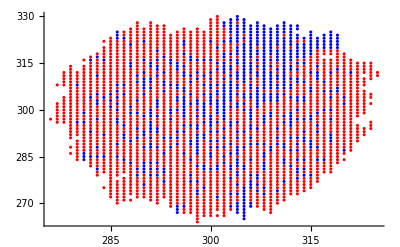

```mathematica
ListPlot[{firstsnaptype1,firstsnaptype2},PlotStyle->{Red,Blue}]
```

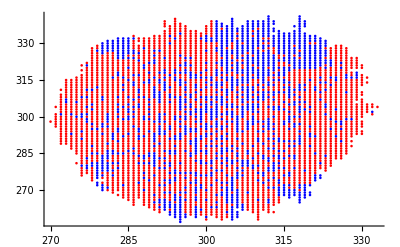

```mathematica
ListPlot[{secondsnaptype1,secondsnaptype2},PlotStyle->{Red,Blue}]
```

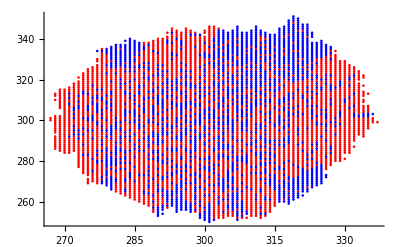

```mathematica
ListPlot[{thirdsnaptype1,thirdsnaptype2},PlotStyle->{Red,Blue}]
```

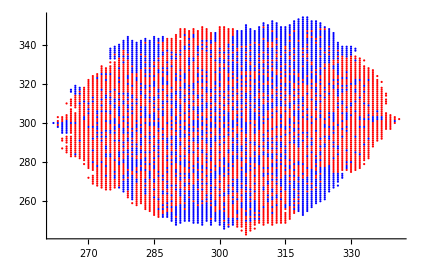

```mathematica
ListPlot[{fourthsnaptype1,fourthsnaptype2},PlotStyle->{Red,Blue}]
```

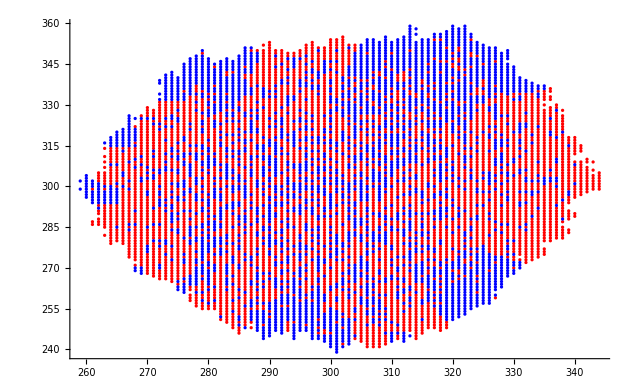

```mathematica
ListPlot[{finalsnaptype1,finalsnaptype2},PlotStyle->{Red,Blue}]
```